```mathematica
d[k_]:=Flatten@ToExpression@StringSplit[Import["./BENCHMARK"][[k]],","];
l = (Length[Import["./BENCHMARK"]]-1)/2;
ll = Length[d[2*l-1]];
y[t_]:=d[2*l-1][[Floor[ll*t/252]+1]];
lll = Length[d[2*l+1]];
yy[t_]:=d[2*l+1][[Floor[lll*t/252]+1]];
```

ToExpression::sntxi: Incomplete expression; more input is needed .

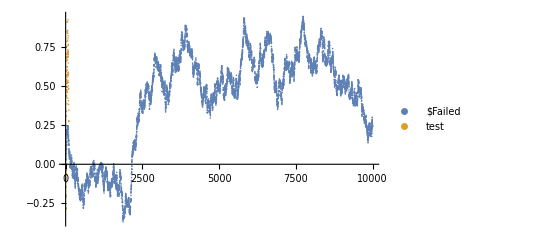

```mathematica
ListPlot[Table[d[2*k+1],{k,1,l}],PlotLegends->Table[d[2*k][[1]],{k,1,l}],PlotRange->Full]
```

Part::partw: Part 10001 of {-0.00407073,-0.011641,-0.029335,-0.0127572,-0.0110412,-0.00721103,-0.0142484,-0.0100823,-0.0102448,-0.0315823,-0.0443536,-0.0292136,-0.0299539,-0.028981,-0.0247082,«21»,-0.0111543,-0.0212784,-0.015274,-0.0105775,-0.00877372,-0.0101404,-0.0234514,-0.0370192,-0.0388816,-0.0444522,-0.0559833,-0.0572287,-0.0601148,-0.0596085,«9950»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

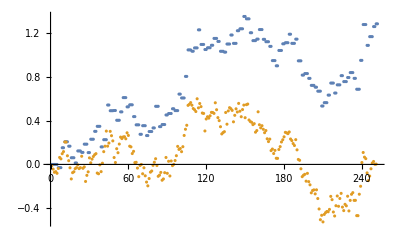

```mathematica
ListPlot[{Table[yy[t],{t,0,251}],Table[y[t],{t,1,252}]}]
```

```mathematica
dt=252/ll*252//N
```

6.3504

```mathematica
ll
```

10000